# Homework 2

## Question 5

### Part C

Using the initial condition to solve for a(c)

```mathematica
IC[c_] := Integrate[Exp[-Power[x,2]-I*c*x],{x,-∞,∞}]
IC[c]
```

ⅇ^(-c^2/4) √π

Plugging a(c) into Part A we get:

```mathematica
exact[x_,t_] := Simplify[Divide[1,2*Pi]*Integrate[IC[c]* Exp[-I * Power[c,2]*t+I*c*x],{c,-∞,∞},Assumptions->t ∈Reals]]
exact[x,t]
```

(ⅇ^(x^2/(-1-4 ⅈ t)))/(√(1+4 ⅈ t))

Plugging a(c) into Part B we get:

```mathematica
aprox[x_,t_] := Divide[Exp[-Divide[x^2,16t^2] + I * Divide[x^2,4t] - I *Divide[Pi,4]],2*Sqrt[t]]
aprox[x,t]
```

(ⅇ^(-(ⅈ π)/4-x^2/(16 t^2)+(ⅈ x^2)/(4 t)))/(2 √t)

Plots x/t = 1
Real

```mathematica
(* Computed graphs individually first to see the difference in computation time
Plot[Re[aprox[t,t]], {t,0,200}]
Plot[Re[exact[t,t]], {t,0,200}]
Plot[Im[aprox[t,t,]], {t,0,200}]
Plot[Im[exact[t,t,]], {t,0,200}]
*)
```

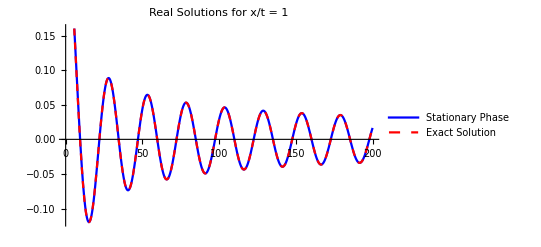

```mathematica
Plot[{Re[aprox[t,t]],Evaluate[Simplify[ComplexExpand[Re[exact[t,t]]]]]},{t,0,200},
PlotLabel -> "Real Solutions for x/t = 1",
PlotLegends->Placed[{"Stationary Phase","Exact Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red]}]
```

Imaginary

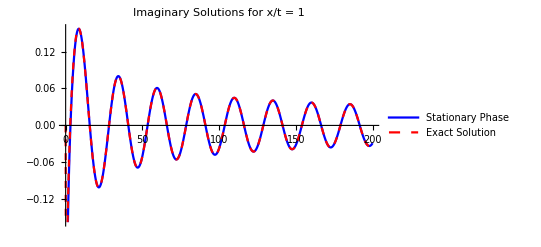

```mathematica
Plot[{Im[aprox[t,t]],Evaluate[Simplify[ComplexExpand[Im[exact[t,t]]]]]},{t,0,200},
PlotLabel -> "Imaginary Solutions for x/t = 1",
PlotLegends->Placed[{"Stationary Phase","Exact Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red]}]
```

Plot x/t = 2
Real

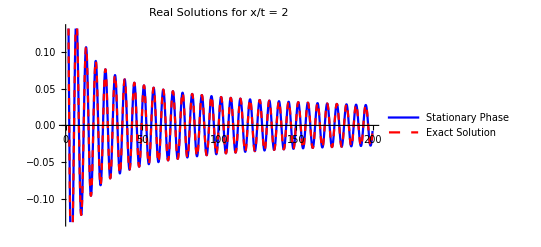

```mathematica
Plot[{Re[aprox[2t,t]],Evaluate[Simplify[ComplexExpand[Re[exact[2t,t]]]]]},{t,0,200},
PlotLabel -> "Real Solutions for x/t = 2",
PlotLegends->Placed[{"Stationary Phase","Exact Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red]}]
```

Imaginary

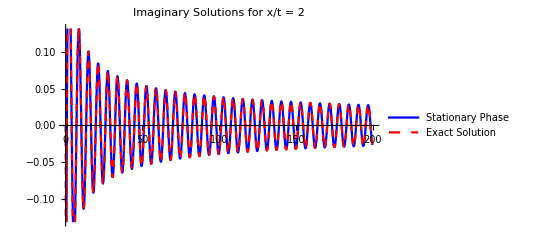

```mathematica
Plot[{Im[aprox[2t,t]],Evaluate[Simplify[ComplexExpand[Im[exact[2t,t]]]]]},{t,0,200},
PlotLabel -> "Imaginary Solutions for x/t = 2",
PlotLegends->Placed[{"Stationary Phase","Exact Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red]}]
```

### Part D

Compute Numerical Exact Solution

```mathematica
Numexact[x_?NumericQ,t_?NumericQ] := Divide[1,2*Pi]*NIntegrate[Exp[-Divide[c^2,4]*Sqrt[Pi]]* Exp[-I * Power[c,2]*t+I*c*x],{c,-∞,∞}, Method ->{"GlobalAdaptive","SymbolicProcessing" -> 0}]
```

Compare Plots

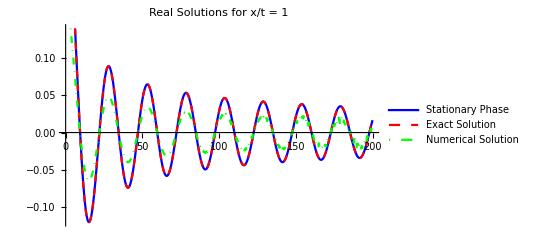

```mathematica
Plot[{Re[aprox[t,t]],Evaluate[Simplify[ComplexExpand[Re[exact[t,t]]]]], Re[Numexact[t,t]]},{t,0,200},
PlotLabel -> "Real Solutions for x/t = 1",
PlotLegends->Placed[{"Stationary Phase","Exact Solution","Numerical Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red], Directive[DotDashed, Green]}]
```

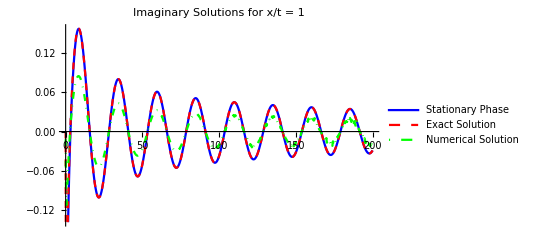

```mathematica
Plot[{Im[aprox[t,t]],Evaluate[Simplify[ComplexExpand[Im[exact[t,t]]]]], Im[Numexact[t,t]]},{t,0,200},
PlotLabel -> "Imaginary Solutions for x/t = 1",
PlotLegends->Placed[{"Stationary Phase","Exact Solution","Numerical Solution"},Below],
PlotStyle->{Directive[Thick, Blue], Directive[Dashed, Red], Directive[DotDashed, Green]}]
```